### 平面上有a, b, c三个点，∡apb = ∠bpc，p点的轨迹是什么

```mathematica
p={x,y};
a={1,2};
b={1,1};
c={1,-2};
va=p-a;vb=p-b;vc=p-c;
equ=(va.vb)/Norm[va]==(vc.vb)/Norm[vc]
```

((-1+x)^2+(-2+y) (-1+y))/(√(Abs[-1+x]^2+Abs[-2+y]^2))==((-1+x)^2+(-1+y) (2+y))/(√(Abs[-1+x]^2+Abs[2+y]^2))

```mathematica
%//FullSimplify
```

```mathematica
((3+(-2+x) x+(-3+y) y)/(√((-1+x)^2+(-2+y)^2)))^2==((-1+(-2+x) x+y+y^2)/(√((-1+x)^2+(2+y)^2)))^2
```

(3+(-2+x) x+(-3+y) y)^2/((-1+x)^2+(-2+y)^2)==((-1+(-2+x) x+y+y^2)^2)/((-1+x)^2+(2+y)^2)

```mathematica
%//FullSimplify
```

((-1+x) (5+(-2+x) x+(-5+y) y))/((5+(-2+x) x)^2+2 (-3+x) (1+x) y^2+y^4)==0

```mathematica
(-1+x) (5+(-2+x) x+(-5+y) y)//Simplify
```

(-1+x) (5+(-2+x) x+(-5+y) y)

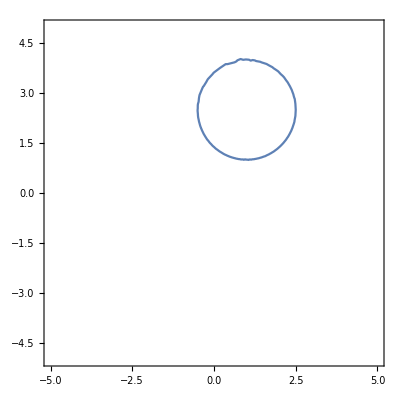

```mathematica
ContourPlot[Evaluate@equ,{x,-5,5},{y,-5,5}]
```

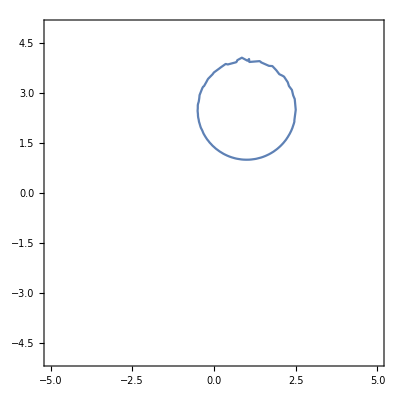

```mathematica
ContourPlot[Evaluate@equ,{x,-5,5},{y,-5,5}]
```

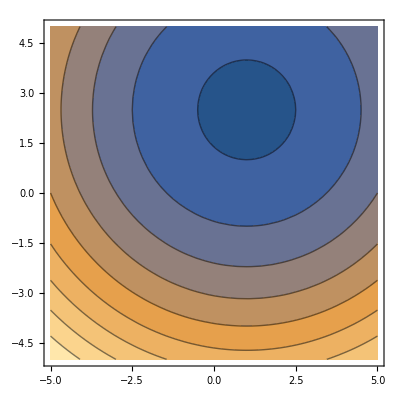

```mathematica
ContourPlot[ (5+(-2+x) x+(-5+y) y),{x,-5,5},{y,-5,5}]
```

```mathematica
(5+(-2+x) x+(-5+y) y)==0/.x->Cos[t]
```

5+(-5+y) y+(-2+Cos[t]) Cos[t]==0

```mathematica
Solve[5+(-5+y) y+(-2+Cos[t]) Cos[t]==0,y]
```

{{y→1/2 (5-√(3+8 Cos[t]-2 Cos[2 t]))},{y→1/2 (5+√(3+8 Cos[t]-2 Cos[2 t]))}}

### 其实，我们可以反向思考这个问题 假设如图

```mathematica
pts={a,p,b,c}={Cos[t],Sin[t]}/.{{t->0},{t->(2.5π)/3},{t->(2π)/3},{t->(4π)/3}};
Graphics[{Circle[],Line[{p,a}],Line[{p,b}],Line[{p,c}],Magenta,PointSize[Large],Point[pts]}]
```

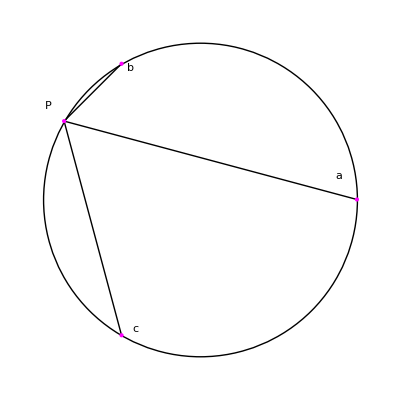

### 显而易见，弧bc上任意一点p, 都满足∠apb = ∠apc

### 如果abc在一条直线上呢